# QHD-2 Tunneling Escape from a Metastable State

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

Second Order Quantized Hamilton Dynamics (QHD-2) is applied to the tunneling escape from a cubic potential. QHD-2 gives an approximation to the Heisenberg Equations of Motion (EOM). The QHD commands used in this document are included in QUANTUM, which is a free Mathematica add-on that can be downloaded from
 http://homepage.cem.itesm.mx/lgomez/quantum/
This tutorial shows how to use the QUANTUM Mathematica add-on to reproduce the results and graphs from Prezhdo and Pereverzev in J. Chem. Phys. Vol 113 No. 16, October 2000, Pages 6557-6565
 http://homepage.cem.itesm.mx/lgomez/quantum/QHD2000.pdf
.

## Load the Package

First load the Quantum`QHD` package. Write:
Needs["Quantum`QHD`"]
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package and print a welcome message:

```mathematica
Needs["Quantum`QHD`"]
```

Quantum`QHD` 
A Mathematica package for Quantized Hamilton Dynamics approximation to Heisenberg Equations of Motion
by José Luis Gómez-Muñoz
based on the original idea of Kirill Igumenshchev

This add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.

Execute SetQHDAliases[] in order to use the keyboard to enter QHD objects
SetQHDAliases[] must be executed again in each new notebook that is created

In order to use the keyboard to enter quantum objects write:
SetQHDAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. Remember that SetQuantumAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetQHDAliases[]
```

ALIASES:
[ESC]on[ESC]     · Quantum concatenation symbol
[ESC]time[ESC]   𝓉 Time symbol
[ESC]hb[ESC]     ℏ Reduced Planck's constant (h bar)
[ESC]ii[ESC]     ⅈ Imaginary I symbol
[ESC]inf[ESC]    ∞ Infinity symbol
[ESC]->[ESC]     → Option (Rule) symbol
[ESC]ave[ESC]    ⟨□⟩ Quantum average template
[ESC]expec[ESC]  ⟨□⟩ Quantum average template
[ESC]symm[ESC]   (□·□)_𝓈 Symmetrized quantum product template
[ESC]comm[ESC]   ⟦□,□⟧_- Commutator template
[ESC]po[ESC]     (□)^□ Power template
[ESC]su[ESC]     □_□ Subscripted variable template
[ESC]posu[ESC]   □_□^□ Power of a subscripted variable template
[ESC]fra[ESC]    □/□ Fraction template
[ESC]eva[ESC]    □/.{□→□,□→□} Evaluation (ReplaceAll) template

SetQHDAliases[] must be executed again in each new notebook that is created, only one time per notebook.

## Potential Energy

The potential energy that will be used in this document is
V=q^2/2+a q^3,  with    a=0.1
It is used by Prezhdo and Pereverzev in J. Chem. Phys. Vol 113 No. 16, October 2000, Pages 6557-6565
 http://homepage.cem.itesm.mx/lgomez/quantum/QHD2000.pdf
This potential energy is used to study tunneling escape with QHD, see the graph below:

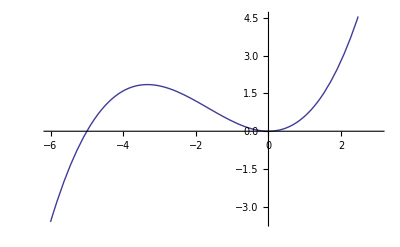

```mathematica
Plot[q^2/2+0.1*q^3,{q,-6,3}]
```

## Commutation Relationships and Hamiltonian

Here we define Hamiltoninan (and store it in the variable th) and commutation relationships that will be used in this document.
In order to enter the templates and symbols □/□, ⟦□,□⟧_- and ⅈ you can either use the QHD palette (toolbar) or press the keys [ESC]fra[ESC], [ESC]comm[ESC] and [ESC]ii[ESC]

```mathematica
Clear[a,p,q];
SetQuantumObject[q,p];
⟦q,p⟧_-=ⅈ;
th=p^2/2+q^2/2+a*q^3
```

p^2/2+q^2/2+a q^3

## Heisenberg Equations of Motion (EOM)

The evolution of the expected value of an observable A in the Heisenberg representation is given by the equation of motion (EOM): 
 ⅈ ℏ d/dt⟨A⟩=⟨[A,H]⟩
The Heisenberg EOM can be calculated using the QHD-Mathematica command QHDEOM, as shown below. The first argument specifies the QHD-order, which is set below to ∞ so that no QHD approximation is made in this first example. The second argument is the observable, which is set to p in the example below. The third argument is the Hamiltonian, remember that it was stored in variable th above in this document. Finally options can be included, for example QHDHBar→1 specifies that reduced Planck’s constant (Dirac constant) will take the value of 1 (The → symbol can be entered by pressing the keys [ESC]->[ESC], that is [ESC][MINUS][GREATERTHAN][ESC]). The output of QHDEOM can be stored in a variable; it is stored in teom below:

```mathematica
teom=QHDEOM[∞,p,th,QHDHBar->1]
```

{{QHDLabel,No closure was applied},{⟨p⟩,-⟨q⟩-3 a ⟨q^2⟩}}

The output of 	QHDEOM can be shown in a nicer format using QHDForm. The output teom that was stored above is formated that way below:

```mathematica
QHDForm[teom]
```

No closure was applied
(d⟨p⟩)/d𝓉=-⟨q⟩-3 a ⟨q^2⟩

On the other hand, the command QHDDifferentialEquations formats the output of QHDEOM as a standard Mathematica equation, as those that can be part of the input of standard Mathematica commands like DSolve and NDSolve. The output teom that was stored above is formated that way below:

```mathematica
QHDDifferentialEquations[teom]
```

{⟨p⟩'[𝓉]==-⟨q⟩[𝓉]-3 a ⟨q^2⟩[𝓉]}

A different symbol for time can be specified. The operator → can be entered pressing the keys [ESC][MINUS][GREATERTHAN][ESC], see the equations below:

```mathematica
QHDDifferentialEquations[teom,QHDSymbolForTime->z]
```

{⟨p⟩'[z]==-⟨q⟩[z]-3 a ⟨q^2⟩[z]}

The EOM for ⟨p⟩ depends on ⟨q⟩ and ⟨q^2⟩ (please remember that ⟨A^2⟩ is NOT the same as ⟨A⟩^2). Next, the EOMs of  ⟨q⟩ and ⟨q^2⟩ can generate new expectation values, such as ⟨p·q⟩_s=⟨(p·q+q·p)/2⟩. Regarding each expectation value as a dynamical variable, we can generate a hierarchy of EOMs, which in general is an infinite hierarchy. We can obtain some of the EOM’s of that infinite hierarchy using the QHD-Mathematica command QHDHierarchy, which has the same syntax as the command QHDEOM that was used above. Likewise, the output of QHDHierarchy can be stored in a variable (tinfhier in the example below) and shown using the command QHDForm below:

```mathematica
tinfhier=QHDHierarchy[∞,p,th,QHDHBar->1];
QHDForm[ tinfhier ]
```

Calculations were stopped at order QHDMaxOrder→2
(d⟨p⟩)/d𝓉=-⟨q⟩-3 a ⟨q^2⟩
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩-⟨q^2⟩-3 a ⟨q^3⟩
(d⟨p^2⟩)/d𝓉=-2 ⟨pq⟩_𝓈-6 a ⟨p q^2⟩_𝓈

A EOM hierarchy can be shown in a graph using the command QHDGraphPlot on the output of QHDHierachy. Arrows point from a first dynamical variable to a second dynamical variable that includes the first one in its EOM; please compare the table above with the graph below:

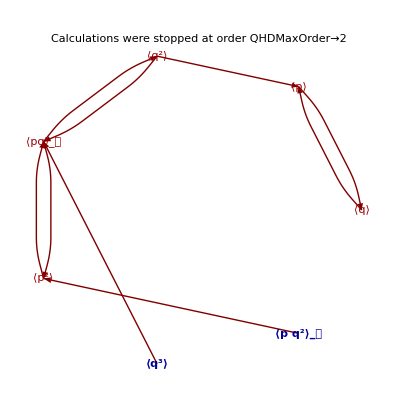

```mathematica
QHDGraphPlot[ tinfhier ]
```

## QHD-2 Closure Approximation

QHDHierarchy stops calculating infinite hierarchies as specified by its option QHDMaxOrder, which takes a default value of 2. Some of the dynamical variables (expectation values) in the truncated hierarchy will not have their equation of motion (EOM) included, as it was shown above by the colors in the ouput of QHDGraphPlot. A closure procedure has to be applied in order to approximate those dynamical variables in terms of those other variables that do have their EOMs included in the hierarchy. For instance, the approximation
⟨ABC⟩≈⟨AB⟩⟨C⟩+⟨AC⟩⟨B⟩+⟨BC⟩⟨A⟩-2⟨A⟩⟨B⟩⟨C⟩
is used to approximate the third-order dynamical variables ⟨q^3⟩ and ⟨pq^2⟩_𝓈 in terms of the first and second order variables ⟨p⟩, ⟨q⟩, ⟨p^2⟩, ⟨q^2⟩ and ⟨p·q⟩_s=⟨(p·q+q·p)/2⟩, thus we obtain a second order QHD finite hierarchy of equations, QHD-2.
The QHD-2 hierarchy is obtained as the output of the command QHDHierarchy with the first argument set to 2. Same as above, the second argument is the first variable in the hierarchy, the third argument is the hamiltonian, and optional arguments can be given after that. The output of QHDHierarchy is stored in the variable thier, and it is shown using the QHDForm command below:

```mathematica
thier=QHDHierarchy[2,p,th,QHDHBar->1];
QHDForm[ thier ]
```

Closure procedure was applied to order 2
(d⟨p⟩)/d𝓉=-⟨q⟩-3 a ⟨q^2⟩
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩+6 a ⟨q⟩^3-⟨q^2⟩-9 a ⟨q⟩ ⟨q^2⟩
(d⟨p^2⟩)/d𝓉=12 a ⟨p⟩ ⟨q⟩^2-6 a ⟨p⟩ ⟨q^2⟩-2 ⟨pq⟩_𝓈-12 a ⟨q⟩ ⟨pq⟩_𝓈

The closed QHD-2 hierarchy can be shown using the QHDGraphPlot command, compare the table above and the graph below:

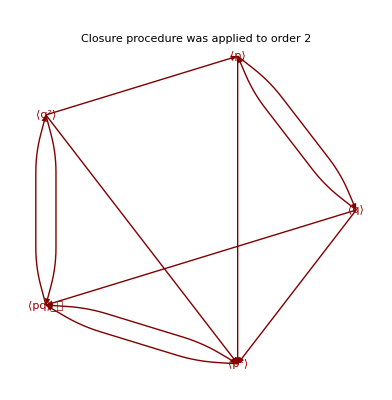

```mathematica
QHDGraphPlot[thier]
```

The command QHDDifferentialEquations formats the output of QHDHierarchy as standard Mathematica equations, as those that can be part of the input of standard Mathematica commands like DSolve and NDSolve. The output thier that was stored above is formated that way below:

```mathematica
QHDDifferentialEquations[thier]
```

{⟨p⟩'[𝓉]==-⟨q⟩[𝓉]-3 a ⟨q^2⟩[𝓉],⟨q⟩'[𝓉]==⟨p⟩[𝓉],⟨q^2⟩'[𝓉]==2 ⟨(p·q)_𝓈⟩[𝓉],⟨(p·q)_𝓈⟩'[𝓉]==⟨p^2⟩[𝓉]+6 a (⟨q⟩[𝓉])^3-⟨q^2⟩[𝓉]-9 a ⟨q⟩[𝓉] ⟨q^2⟩[𝓉],⟨p^2⟩'[𝓉]==12 a ⟨p⟩[𝓉] (⟨q⟩[𝓉])^2-6 a ⟨p⟩[𝓉] ⟨q^2⟩[𝓉]-2 ⟨(p·q)_𝓈⟩[𝓉]-12 a ⟨q⟩[𝓉] ⟨(p·q)_𝓈⟩[𝓉]}

## Solution of the QHD-2 Equations: Tunneling

Next we evaluate the hierarchy when the parameter a takes the value of 0.1, and the result of that evaluation is stored in the variable tnumhier:

```mathematica
tnumhier= thier/. {a->0.1};
QHDForm[tnumhier]
```

Closure procedure was applied to order 2
(d⟨p⟩)/d𝓉=-⟨q⟩-0.3 ⟨q^2⟩
(d⟨q⟩)/d𝓉=⟨p⟩
(d⟨q^2⟩)/d𝓉=2 ⟨pq⟩_𝓈
(d⟨pq⟩_𝓈)/d𝓉=⟨p^2⟩+0.6 ⟨q⟩^3-⟨q^2⟩-0.9 ⟨q⟩ ⟨q^2⟩
(d⟨p^2⟩)/d𝓉=1.2 ⟨p⟩ ⟨q⟩^2-0.6 ⟨p⟩ ⟨q^2⟩-2 ⟨pq⟩_𝓈-1.2 ⟨q⟩ ⟨pq⟩_𝓈

The command QHDInitialConditionsTemplate generates an initial conditions template for the hierarchy:

```mathematica
QHDInitialConditionsTemplate[tnumhier , 0]
```

{⟨p⟩[0]==■,⟨q⟩[0]==■,⟨q^2⟩[0]==■,⟨(p·q)_𝓈⟩[0]==■,⟨p^2⟩[0]==■}

Copy-paste the output of the previous command as input in the next one. Fill in the placeholders (■) with the appropiate initial values. Those initial values can be numbers. On the other hand, in the calculation below they are symbols like po, and then these symbols are evaluated at the desired numerical values. These initial conditions correspond to a Gaussian wavepacket, with its center one unit to the left of the minimum of the potential energy, and its momentum pointing to the right hand side, see  J. Chem. Phys. Vol 113 No. 16, October 2000, Pages 6557-6565
 http://homepage.cem.itesm.mx/lgomez/quantum/QHD2000.pdf
The initial conditions are stored in the variable tinicond below:

```mathematica
tinicond={⟨p⟩[0]==po,⟨q⟩[0]==qo,⟨q^2⟩[0]==qo^2+1/2,⟨Subscript[(p·q), 𝓈]⟩[0]==po*qo,⟨p^2⟩[0]==po^2+1/2}/. 
{ po->1.0, qo->-1.0}
```

{⟨p⟩[0]==1.,⟨q⟩[0]==-1.,⟨q^2⟩[0]==1.5,⟨(p·q)_𝓈⟩[0]==-1.,⟨p^2⟩[0]==1.5}

The command QHDNDSolve takes as arguments the numerical version of the hierarchy (which was stored in the variable tnumhier), the initial conditions (which were stored in tinicond), the initial time and the final time. The output of this command is the numerical solution of the differential equations, in the form of InterpolatingFunction objects. This output can be used to plot (graph) the dynamical variables as functions of time, as it will be shown below in this document. The output is stored in the variable tsol in the calculation below:

```mathematica
tsol=QHDNDSolve[tnumhier,tinicond,0,9]
```

{{⟨p⟩→InterpolatingFunction[{{0.,9.}},<>],⟨q⟩→InterpolatingFunction[{{0.,9.}},<>],⟨q^2⟩→InterpolatingFunction[{{0.,9.}},<>],⟨(p·q)_𝓈⟩→InterpolatingFunction[{{0.,9.}},<>],⟨p^2⟩→InterpolatingFunction[{{0.,9.}},<>]}}

The command command QHDPlot takes as its second argument the output of QHDNDSolve, which was stored in the variable tsol. The first argument specifies the dynamical variables or expression that we want to plot (graph) as a function of time. If we want to plot all the dynamical variables, the first argument must be the word All, see the five plots below:

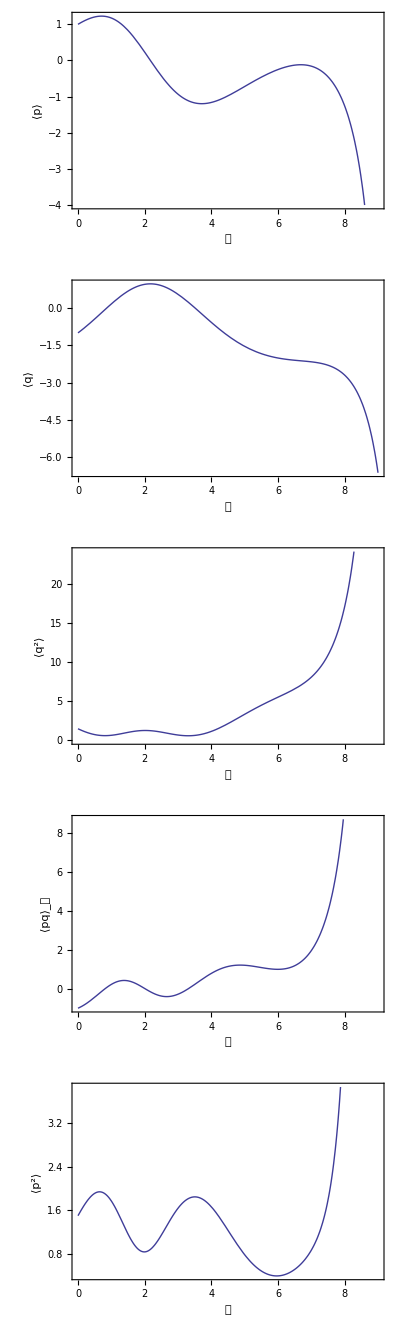

```mathematica
QHDPlot[All,tsol]
```

Next command generates the plot of ⟨q⟩ as a function of time and stores it in the variable tpos. This plot stored in the variable tpos will be used again at the end of this document.
This evolution of ⟨q⟩ as a function of time shows a tunneling event, because ⟨q⟩ leaves the basin of the local minimum of the potential. This will be clearly shown at the end of the document, where classical dynamics is compared with this QHD-2 dynamics.

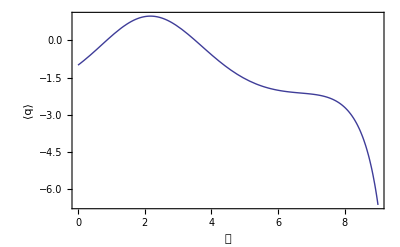

```mathematica
tpos=QHDPlot[q,tsol]
```

QHDPlot can be used to plot functions of the dynamical variables, for example the “spread” of the wavepacket √(⟨q^2⟩-⟨q⟩^2). The ⟨□⟩ template can be entered using the QHD palette (toolbar), or pressing the keys [ESC]expec[ESC], or pressing the keys [ESC]ave[ESC]. The interpretation of the plot below is that the wavepacket mantains its width till the tunneling event, which roughly begins at t=4, as can be seen below:

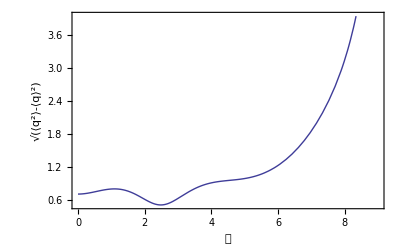

```mathematica
QHDPlot[√(⟨q^2⟩-⟨q⟩^2),tsol]
```

On the other hand, the “spread” in momentum √(⟨p^2⟩-⟨p⟩^2) is very small during tunneling, roughly for 4<𝓉<6, see the graph below:

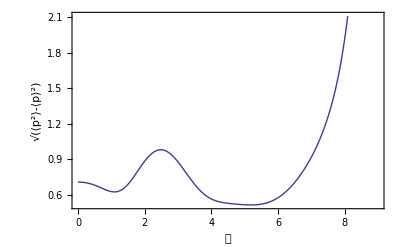

```mathematica
QHDPlot[√(⟨p^2⟩-⟨p⟩^2),tsol]
```

QHDParametricPlot can be used to generate phase-space plots of couples of dynamical variables. The plot (graph) below is stored in the variable tphase, in order to be used again at the end of this document:

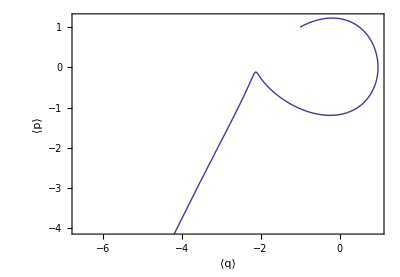

```mathematica
tphase=QHDParametricPlot[{q,p},tsol]
```

Next the command QHDClosure is used to obtain the QHD-2 expression for the energy of the system, and it is stored in the variable tenergy below:

```mathematica
tenergy=QHDClosure[2,p^2/2+q^2/2+a*q^3]
```

⟨p^2⟩/2-2 a ⟨q⟩^3+⟨q^2⟩/2+3 a ⟨q⟩ ⟨q^2⟩

This is a numerical version of the QHD-2 expresson for the energy. It is stored in the variables tnumenergy below:

```mathematica
tnumenergy=tenergy/.{a->0.1}
```

⟨p^2⟩/2-0.2 ⟨q⟩^3+⟨q^2⟩/2+0.3 ⟨q⟩ ⟨q^2⟩

QHDPlot is used to plot the QHD-2 energy. The numerical solution of the differential equations is very good at keeping the energy constant before the tunneling event. Even after the tunneling the variation of the QHD-2 energy is very small, see the scale in the left hand side of the frame below:

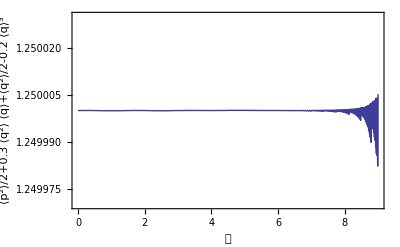

```mathematica
QHDPlot[tnumenergy,tsol,PlotRange->{1.24997,1.25003}]
```

## QHD-2 for Lower Energies

Here the numerical solution of the hierarchy (system of equations) stored in the variable tnumhier is obtained for a different set of initial conditions. Again they represent a Gaussian wavepacket, but this time the initial position is at the minimum of the potential energy. Notice that the solution with these initial conditions is stored in the variables tsol2 below. The phase-space plot produced by QHDParametricPlot shows that this time there is no tunneling event, with the wavepacket only oscillating about the minimum of the potential energy, see the graph below:

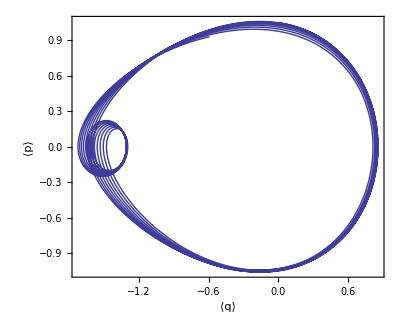

```mathematica
tinicond2={
⟨p⟩[0]==po,
⟨q⟩[0]==qo,
⟨p^2⟩[0]==po^2+1/2,
⟨Subscript[(p·q), 𝓈]⟩[0]==po*qo,
⟨q^2⟩[0]==qo^2+1/2} /. 
{ po->1.05, qo->0};

tsol2=QHDNDSolve[tnumhier,tinicond2,0,100];

QHDParametricPlot[{q,p},tsol2]
```

The command QHDParametricPlot3D can be used to generate 3D phase plots. Here the position ⟨q⟩, momentum ⟨p⟩ and “spread” ⟨q^2⟩-⟨q⟩^2 are shown for the numerical solution that was stored in tsol2. The ⟨□⟩ template can be entered using the QHD palette (toolbar), or pressing the keys [ESC]expec[ESC], or pressing the keys [ESC]ave[ESC].

```mathematica
QHDParametricPlot3D[{q,p,⟨q^2⟩-⟨q⟩^2},tsol2]
```

-Graphics3D-

Here the hierarchy (system of equations) that was stored in tnumhier and the initial conditions that were stored in tinicond2 are used to generate a graph that can be compared with the corresponding graph in the paper by Prezhdo and Pereverzev. Notice that QHDParametricPlot accepts the same options as the standard Mathematica command ParametricPlot, see the graph below:

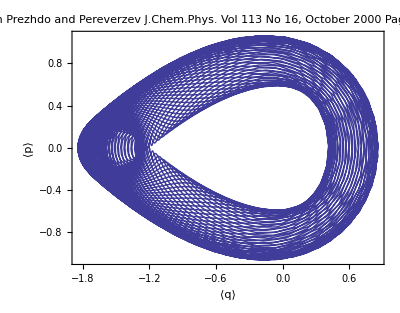

```mathematica
tsol3=QHDNDSolve[tnumhier,tinicond2,0,700];

QHDParametricPlot[{q,p},tsol3,PlotStyle->Thin,PlotLabel->"Compare with Prezhdo and Pereverzev \nJ.Chem.Phys. Vol 113 No 16, October 2000\nPages 6557-6565 Fig. 4(b)"]
```

Here the expression for the QHD-2 energy, which was stored in the variable tnumenergy and the numerical solution that was stored in the variable tsol3 are used to show that the numerical solution of the differential equations is very good at keeping the energy constant, see the graph below:

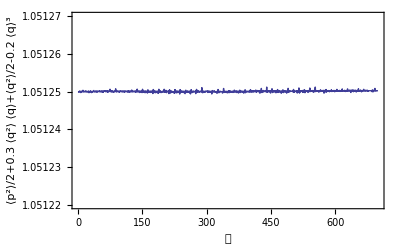

```mathematica
QHDPlot[tnumenergy,tsol3,PlotRange->{1.05122,1.05127}]
```

## Classical Dynamics (QHD-1) for the Same Hamiltonian

The first-order QHD equations are actually the same as those of classical dynamics for a single particle. Please remember that the Hamiltonian was stored in the variable th. The QHD-1 hierarchy (made only of two EOMs, for position and momentum) is stored in the variable classicthier below:

```mathematica
classicthier=QHDHierarchy[1,p,th,QHDHBar->1];
QHDForm[ classicthier ]
```

Closure procedure was applied to order 1
(d⟨p⟩)/d𝓉=-⟨q⟩-3 a ⟨q⟩^2
(d⟨q⟩)/d𝓉=⟨p⟩

Next we evaluate the hierarchy when the parameter a takes the value of 0.1, and the result of that evaluation is stored in the variable numclassichier below:

```mathematica
numclassicthier= classicthier/. {a->0.1};
QHDForm[ numclassicthier ]
```

Closure procedure was applied to order 1
(d⟨p⟩)/d𝓉=-⟨q⟩-0.3 ⟨q⟩^2
(d⟨q⟩)/d𝓉=⟨p⟩

The command QHDInitialConditionsTemplate generates a template for the initial conditions for the hierarchy:

```mathematica
QHDInitialConditionsTemplate[numclassicthier,0]
```

{⟨p⟩[0]==■,⟨q⟩[0]==■}

Copy-paste the output of the previous command as input in the next one. Fill in the placeholders (■) with the appropiate initial values. The initial conditions are stored in the variable tiniclassical and used as the second argument of the command QHDNDSolve below. The first argument is the hierarchy numclassichier, and the numerical solution is stored in the variable tclassicsol below:

```mathematica
tiniclassical={⟨p⟩[0]==1.0,⟨q⟩[0]==-1.0};
tclassicsol=QHDNDSolve[numclassicthier,tiniclassical,0,9]
```

{{⟨p⟩→InterpolatingFunction[{{0.,9.}},<>],⟨q⟩→InterpolatingFunction[{{0.,9.}},<>]}}

The plot of the position variable q for the classical solution tclassicsol is stored in the variable tposcla, it will be used again at the end of this document:

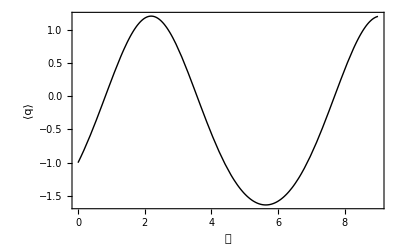

```mathematica
tposcla=QHDPlot[q,tclassicsol,PlotStyle->Black]
```

The phase-space plot for the classical solution tclassicsol is stored in the variable tphasecla, it will be used again at the end of this document:

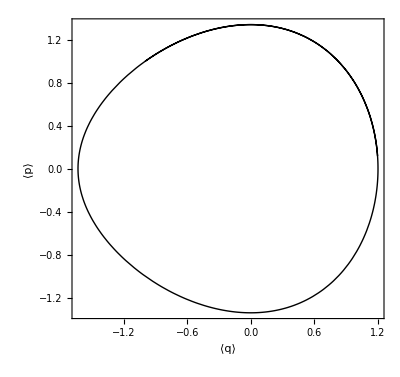

```mathematica
tphasecla=QHDParametricPlot[{q,p},tclassicsol,PlotStyle->Black]
```

## Compare Classical Dynamics (QHD-1) with QHD-2

Here we compare the classical dynamics solution (tposcla) with the QHD-2 solution (tpos). They begin oscillating together, however about t=5 the QHD-2 solution shows a tunneling event, while the classical solution continues oscillating, see the graph below:

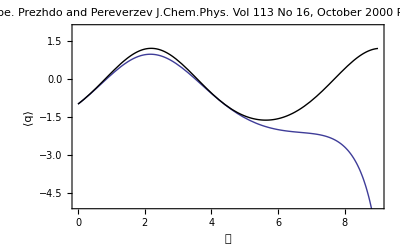

```mathematica
Show[tpos,tposcla,
PlotRange->{-5,2},
PlotLabel->"Tunneling Escape. Prezhdo and Pereverzev\nJ.Chem.Phys. Vol 113 No 16, October 2000\nPages 6557-6565 Fig. 2(b)"]
```

Here we compare the classical dynamics solution (tposcla) with the QHD-2 solution (tpos). They begin oscillating together, however the QHD-2 solution shows a tunneling event, while the classical solution continues oscillating, see the graph below:

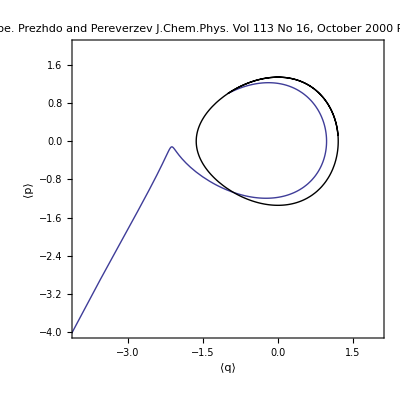

```mathematica
Show[tphase,tphasecla,
PlotRange->{{-4,2},{-4,2}},
PlotLabel->"Tunneling Escape. Prezhdo and Pereverzev \nJ.Chem.Phys. Vol 113 No 16, October 2000\nPages 6557-6565 Fig. 3(b)"]
```

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx